```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Tue 23 May 2023 10:22:19

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 17 edited by Chi-Ok Hwang, originally made by Dr. 전 경원 and Prof. 정 영주

[1] C. Arangala, Exploring Linear Algebra: Labs and Projects with Mathematica ®, 1st ed. Boca Raton: Chapman and Hall/CRC, 2014.

-Graphics-

(SC) Practice

```mathematica
Solve[a x + b == c, x]
```

{{x→(-b+c)/a}}

```mathematica
SCDivEq[ a x + b == c, a ]
```

b/a+x==c/a

```mathematica
SCSubtFromEq[%, b/a ]
```

x==-b/a+c/a

```mathematica
SCSimpExp[%]
```

{{x→(-b+c)/a}}

```mathematica
SCEqSolve[a x + b == c, x]
```

{{x→(-b+c)/a}}

### Solution of the quadratic equation a x^2+b x+c=0

Divide the left-hand side with a.

x^2+(b x)/a+c/a=0    ⟶    x^2+(b x)/a=-c/a

Expand (x+b/(2a))^2 and use the above relation

(x+b/(2a))^2=x^2+(b x)/a+b^2/(4 a^2)=-c/a+b^2/(4 a^2)=(b^2-4a c)/(4 a^2)

Therefore, the roots for x are

x=-b/(2a)±(√(b^2-4a c))/(2a)=(-b±√(b^2-4a c))/(2a)

Obtain the solution for x by applying a series of functions to the equation as summarized below.

```mathematica
Grid[{{"Function","Equation","Comment"},
{,a x^2+b x+c==0,"Quadratic equation"},
{SCMergePoly,-b^2/(4 a)+c+a (b/(2 a)+x)^2==0,"Eliminate the first order term."},
{SCSolve,(b/(2 a)+x)^2==(b^2-4 a c)/(4 a^2),"Solve for (b/(2 a)+x)^2."},
{SCEqMap,x==-b/(2 a)+(±1/2) (√(b^2-4 a c))/a,"Solution for x"},
{Together,x==(-b+(±1) √(b^2-4 a c))/(2 a),"Rearrange the result"}},ItemSize->{{8,15,20}},Frame->All]
```

Function | Equation | Comment
 | c+b x+a x^2==0 | Quadratic equation
SCMergePoly | -b^2/(4 a)+c+a (b/(2 a)+x)^2==0 | Eliminate the first order term.
SCSolve | (b/(2 a)+x)^2==(b^2-4 a c)/(4 a^2) | Solve for (b/(2 a)+x)^2.
SCEqMap | x==-b/(2 a)+(±1/2) (√(b^2-4 a c))/a | Solution for x
Together | x==(-b+(±1) √(b^2-4 a c))/(2 a) | Rearrange the result

```mathematica
a x^2+b x+c==0
SCMAF[%,SCMergePoly,{At[1],x},
SCSolve,{All,(b/(2 a)+x)^2},
SCEqMap,{All,√#&},Post->PowerExpand,Post->{At[2],SCMultiply->(±1)},PostAll->{Together,SCEqMove->x},
Trace->True]
```

c+b x+a x^2==0

-b^2/(4 a)+c+a (b/(2 a)+x)^2==0

(b/(2 a)+x)^2==(b^2-4 a c)/(4 a^2)

x==(-b+(±1) √(b^2-4 a c))/(2 a)

Vector Operators

• The vector operators built in the Mathematica kernel
  – Expressions are evaluated immediately.

```mathematica
Grad[x^2*y*z, {x,y,z},"Cartesian"]
```

{2 x y z,x^2 z,x^2 y}

```mathematica
Div[{ρ^2 Sin[ϕ],ρ^2 Cos[ϕ],ρ z},{ρ,ϕ,z},"Cylindrical"]//Expand
```

ρ+2 ρ Sin[ϕ]

```mathematica
Curl[{r^2 Sin[θ],r^2 Cos[θ],0},{r,θ,ϕ},"Spherical"]
```

{0,0,2 r Cos[θ]}

```mathematica
Laplacian[x^2 y z,{x,y,z}]
```

2 y z

```mathematica
Laplacian[{x^2,y z,x+z},{x,y,z}]
```

{2,0,0}

◀     |     ▶

Example: Mode Coupling in Mechanical Systems

• Two coupled harmonic oscillators with the resonance frequency ω. The coupling is represented by δ.

-Graphics-

• The equations of motion with the coupling parameter δ. ω is the resonance frequency of the harmonic oscillators.

```mathematica
SCEqMove[(ⅆ^2 Subscript[x, 1])/(ⅆ t^2)+ω^2 Subscript[x, 1]-δ^2(Subscript[x, 2]-Subscript[x, 1])==0,(ⅆ^2 Subscript[x, 1])/(ⅆ t^2)]
SCEqMove[{(ⅆ^2 Subscript[x, 1])/(ⅆ t^2)+ω^2 Subscript[x, 1]-δ^2(Subscript[x, 2]-Subscript[x, 1])==0,(ⅆ^2 Subscript[x, 2])/(ⅆ t^2)+ω^2 Subscript[x, 2]+δ^2(Subscript[x, 2]-Subscript[x, 1])==0},{(ⅆ^2 Subscript[x, 1])/(ⅆ t^2),(ⅆ^2 Subscript[x, 2])/(ⅆ t^2)}]
```

(ⅆ^2 x_1)/(ⅆ t^2)==-ω^2 x_1+δ^2 (-x_1+x_2)

{(ⅆ^2 x_1)/(ⅆ t^2)==-ω^2 x_1+δ^2 (-x_1+x_2),(ⅆ^2 x_2)/(ⅆ t^2)==-ω^2 x_2-δ^2 (-x_1+x_2)}

```mathematica
ClearAll["Global`*"]
ρ[x,t]==Abs[Ψ[x,t]]^2
SCMAF[%,RA,{At[2],Ψ[x,t]==Subscript[a, 2] Subscript[Ψ, 2][x,t]+Subscript[a, 3] Subscript[Ψ, 3][x,t]}]
```

ρ[x,t]==(|Ψ[x,t]|)^2

ρ[x,t]==(|a_2 Ψ_2[x,t]+a_3 Ψ_3[x,t]|)^2

```mathematica
ClearAll["Global`*"]
{(ⅆ^2 Subscript[x, 1])/(ⅆ t^2)+ω^2 Subscript[x, 1]-δ^2(Subscript[x, 2]-Subscript[x, 1])==0,(ⅆ^2 Subscript[x, 2])/(ⅆ t^2)+ω^2 Subscript[x, 2]+δ^2(Subscript[x, 2]-Subscript[x, 1])==0}
SCMAF[%,SCEqMove,{All,{(ⅆ^2 Subscript[x, 1])/(ⅆ t^2),(ⅆ^2 Subscript[x, 2])/(ⅆ t^2)}},Level-> 1,
SCEqsMatForm,{All,{Subscript[x, 1],Subscript[x, 2]},Factor->-1},SCMergeDerivs,At[1],
RA,{All,{({{Subscript[x, 1]}, {Subscript[x, 2]}})==x⃗,({{δ^2+ω^2, -δ^2}, {-δ^2, δ^2+ω^2}})==M}}]
```

{(ⅆ^2 x_1)/(ⅆ t^2)+ω^2 x_1-δ^2 (-x_1+x_2)==0,(ⅆ^2 x_2)/(ⅆ t^2)+ω^2 x_2+δ^2 (-x_1+x_2)==0}

ⅆ^2/(ⅆ t^2)(x_1
x_2)==-(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)·(x_1
x_2)

(ⅆ^2 x⃗)/(ⅆ t^2)==-M·x⃗

ClearAll["Global`*"]
{(ⅆ^2 x_1)/(ⅆ t^2)+ω^2 x_1-δ^2(x_2-x_1)==0,(ⅆ^2 x_2)/(ⅆ t^2)+ω^2 x_2+δ^2(x_2-x_1)==0}
SCMAF[%,SCEqMove,{All,{(ⅆ^2 x_1)/(ⅆ t^2),(ⅆ^2 x_2)/(ⅆ t^2)}},Level→ 1,
SCEqsMatForm,{All,{x_1,x_2},Factor→-1},
RA,{All,{(x_1
x_2)==x⃗,(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)==M}}]

{(ⅆ^2 x_1)/(ⅆ t^2)+ω^2 x_1-δ^2 (-x_1+x_2)==0,(ⅆ^2 x_2)/(ⅆ t^2)+ω^2 x_2+δ^2 (-x_1+x_2)==0}

((ⅆ^2 x_1)/(ⅆ t^2)
(ⅆ^2 x_2)/(ⅆ t^2))==-(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)·(x_1
x_2)

((ⅆ^2 x_1)/(ⅆ t^2)
(ⅆ^2 x_2)/(ⅆ t^2))==-M·x⃗

where

M==(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)

M=={{δ^2+ω^2,-δ^2},{-δ^2,δ^2+ω^2}}

• The eigenvalues and eigenvectors of M are

Ω^2==Eigenvalues[(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)]

Ω^2=={ω^2,2 δ^2+ω^2}

v⃗==Eigenvectors[(δ^2+ω^2 | -δ^2
-δ^2 | δ^2+ω^2)]

v⃗=={{1,1},{-1,1}}

We will put

ω_0==√(2 δ^2+ω^2)
SCMAF[%,SCTaylorSeries,{At[2],δ,2},Post→PowerExpand,Head→TildeTilde,Comment→"For small coupling δ"]

Equal[Subscript[\[Omega],0],Power[Plus[Times[2,Power[\[Delta],2]],Power[\[Omega],2]],Rational[1,2]]]

ω_0==√(2 δ^2+ω^2)

For small coupling δ

ω_0≈δ^2/ω+ω

• The solution of the differential equations with the initial conditions x_1(0)=x_10,x_2(0)=0,x_1'(0)=0,x_2'(0)=0

{ω^2 x_1-δ^2 (-x_1+x_2)+(ⅆ^2 x_1)/(ⅆ t^2)==0,ω^2 x_2+δ^2 (-x_1+x_2)+(ⅆ^2 x_2)/(ⅆ t^2)==0}
SCMAF[%,SCDSolve,{All,{x_1[0]==x_(1,0),x_2[0]==0,x_1'[0]==0,x_2'[0]==0},{x_1[t],x_2[t]},t},
SCFactorI,√(-2 δ^2-ω^2),PostAll→ExpandAll,,
RA,{All,√(2 δ^2+ω^2)==ω_0},
SCExpToTrig,All,
Collect,{At[{1,2},{2,2}],x_(1,0),TrigFactor},
SCMapApply,{All,Simplify,{Cos,Sin}},ChangeSign→ω-ω_0]

{(ⅆ^2 x_1)/(ⅆ t^2)+ω^2 x_1-δ^2 (-x_1+x_2)==0,(ⅆ^2 x_2)/(ⅆ t^2)+ω^2 x_2+δ^2 (-x_1+x_2)==0}

{x_1[t]==1/4 ⅇ^(-ⅈ t ω) x_(1,0)+1/4 ⅇ^(ⅈ t ω) x_(1,0)+1/4 ⅇ^(-ⅈ t √(2 δ^2+ω^2)) x_(1,0)+1/4 ⅇ^(ⅈ t √(2 δ^2+ω^2)) x_(1,0),x_2[t]==1/4 ⅇ^(-ⅈ t ω) x_(1,0)+1/4 ⅇ^(ⅈ t ω) x_(1,0)-1/4 ⅇ^(-ⅈ t √(2 δ^2+ω^2)) x_(1,0)-1/4 ⅇ^(ⅈ t √(2 δ^2+ω^2)) x_(1,0)}

{x_1[t]==x_(1,0) Cos[(t ω)/2-(t ω_0)/2] Cos[(t ω)/2+(t ω_0)/2],x_2[t]==-x_(1,0) Sin[(t ω)/2-(t ω_0)/2] Sin[(t ω)/2+(t ω_0)/2]}

{x_1[t]==x_(1,0) Cos[(t ω)/2-(t ω_0)/2] Cos[(t ω)/2+(t ω_0)/2],x_2[t]==-x_(1,0) Sin[(t ω)/2-(t ω_0)/2] Sin[(t ω)/2+(t ω_0)/2]}

The total energy is conserved:

ClearAll["Global`*"]
Ε_tot==Ε_1+Ε_2+V_int
SCMAF[%,RA,{At[2],{Ε_j_→ 1/2 m((ⅆ x_j)/ⅆt)^2+1/2 m ω^2 x_j^2,V_int→ 1/2 m δ^2(x_1-x_2)^2}},
RA,{At[2],{x_1[t]→ Cos[1/2 t (-ω+ω_0)] Cos[1/2 t (ω+ω_0)] x_(1,0),x_2[t]→ Sin[1/2 t (-ω+ω_0)] Sin[1/2 t (ω+ω_0)] x_(1,0)}},SCEvalDeriv, {At[2],Variables → t},Post→Simplify,At[2],
SCTrigToHalf,_Cos,RA,{At[2],ω_0==√(2 δ^2+ω^2)},Post→Simplify]

Ε_tot==V_int+Ε_1+Ε_2

Ε_tot==1/8 m (2 δ^2+3 ω^2+(2 δ^2+ω^2) Cos[2 t ω_0]+2 Sin[t ω_0]^2 ω_0^2) x_(1,0)^2

Ε_tot==1/8 m (2 δ^2+3 ω^2+(2 δ^2+ω^2) Cos[2 t ω_0]+2 Sin[t ω_0]^2 ω_0^2) x_(1,0)^2

• Since

SCARA[{x_1+x_2,x_1-x_2},{x_1[t]==Cos[1/2 t (-ω+ω_0)] Cos[1/2 t (ω+ω_0)] x_(1,0),x_2[t]==Sin[1/2 t (-ω+ω_0)] Sin[1/2 t (ω+ω_0)] x_(1,0)},Post→Simplify,PostAll→Thread]

{x_1+x_2==Cos[t ω] x_(1,0),x_1-x_2==Cos[t ω_0] x_(1,0)}

we have

{|x_1+x_2|≤|x_(1,0)|,|x_1-x_2|≤|x_(1,0)|}

{|x_1+x_2|≤|x_(1,0)|,|x_1-x_2|≤|x_(1,0)|}

This corresponds to the region shaded below:

```mathematica
Plot[1-x,{x,-1,1}]
```

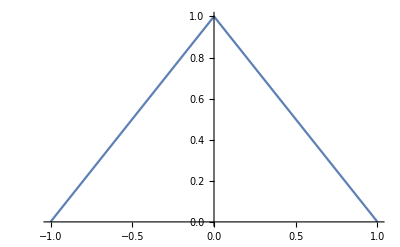

```mathematica
Plot[1-Abs[x],{x,-1,1}]
```

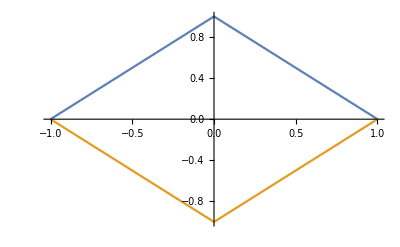

```mathematica
Plot[{1-Abs[x],Abs[x]-1},{x,-1,1}]
```

Plot[{1-Abs[x],Abs[x]-1},{x,-1,1},AspectRatio→1,AxesLabel→{x_1/(x_(1,0)),x_2/(x_(1,0))},Filling→{1→{2}}]

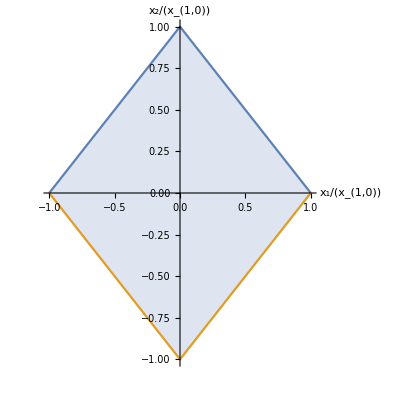

• Motion of the two masses in time t

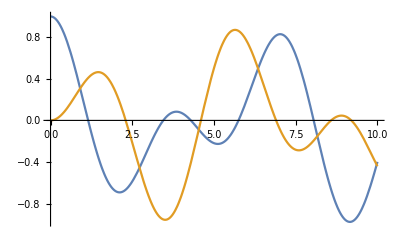

```mathematica
ClearAll["Global`*"]
δ=1;
ω=1;
Plot[ {Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]},{t ,0,10}]
```

```mathematica
ClearAll["Global`*"]
SCRemOp[A·({{a}, {b}}),A]
```

{{a},{b}}

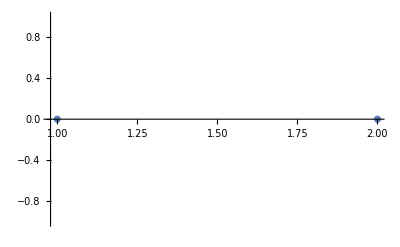

```mathematica
ListPlot[{{2,0},{1,0}}]
```

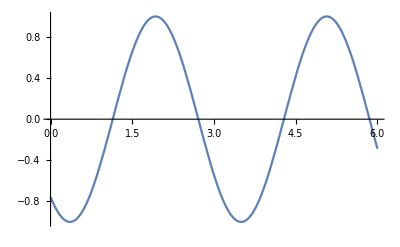

-Graphics-

```mathematica
ClearAll["Global`*"]
Plot[Sin[2x+4],{x,0,6}]
Sin[2x+4];
SCMAF[%,Plot,{All,{x,0,6}}]
```

```mathematica
ClearAll["Global`*"]
Manipulate[Plot[Sin[a x+b],{x,0,6}],{a,1,4},{b,0,10}];
ClearAll["Global`*"]
Sin[a x+b];
SCMAF[%,Plot,{All,{x,0,6}},HoldForm -> True,Manipulate,{All,{a,1,4},{b,0,10}}]
```

Plot[Sin[b+a x],{x,0,6}]

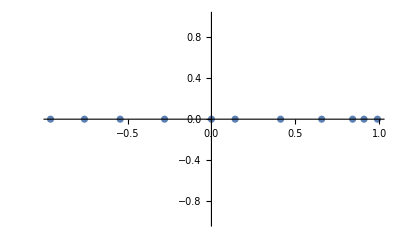

{{0,0},{Sin[1],0},{Sin[2],0},{Sin[3],0},{Sin[4],0},{Sin[5],0},{Sin[6],0},{Sin[7],0},{Sin[8],0},{Sin[9],0},{Sin[10],0}}

-Graphics-

```mathematica
ClearAll["Global`*"]
Table[{Sin[t],0},{t,0,10,1}];
ListPlot[%]
{{0,0},{Sin[1],0},{Sin[2],0},{Sin[3],0},{Sin[4],0},{Sin[5],0},{Sin[6],0},{Sin[7],0},{Sin[8],0},{Sin[9],0},{Sin[10],0}}
ListPlot[%]
```

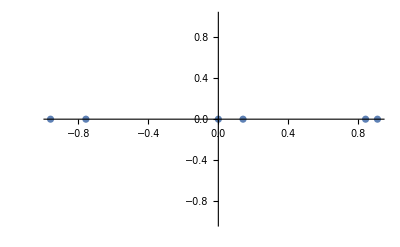

{{0,0},{Sin[1],0},{Sin[2],0},{Sin[3],0},{Sin[4],0},{Sin[5],0}}

-Graphics-

```mathematica
ClearAll["Global`*"]
{#,0}&[Sin[t]];
ListPlot[Table[%,{t,0,5,1}]]
Sin[t] ;
SCMAF[%,{#,0}&,All,Table,{All,{t,0,5,1}},
ListPlot,All]
```

```mathematica
ClearAll["Global`*"]
ListPlot[{{0.,0.},{0.8414709848078965,0.},{0.9092974268256817,0.},{0.1411200080598672,0.},{-0.7568024953079282,0.},{-0.9589242746631385,0.},{-0.27941549819892586,0.},{0.6569865987187891,0.},{0.9893582466233818,0.},{0.4121184852417566,0.},{-0.5440211108893698,0.}}]//FullForm
```

$Aborted

HoldForm[ListPlot[List[List[0.,0.],List[0.841471,0.],List[0.909297,0.],List[0.14112,0.],List[-0.756802,0.],List[-0.958924,0.],List[-0.279415,0.],List[0.656987,0.],List[0.989358,0.],List[0.412118,0.],List[-0.544021,0.]]]]

```mathematica
ClearAll["Global`*"]
ω=1;
δ=2;
Sin[ω/2 (-1+√(1+(2 δ^2)/ω^2))]
N[%]
{{0,0},{Sin[ω/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(3 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(5 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[3 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(7 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[4 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(9 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[5 ω (-1+√(1+(2 δ^2)/ω^2))],0}}
N[%]
```

HoldForm[Times[ClearAll["Global`*"],ListPlot[List[List[0.,0.],List[0.841471,0.],List[0.909297,0.],List[0.14112,0.],List[-0.756802,0.],List[-0.958924,0.],List[-0.279415,0.],List[0.656987,0.],List[0.989358,0.],List[0.412118,0.],List[-0.544021,0.]]]]]

```mathematica
ClearAll["Global`*"]
ListPlot[{{0.,0.},{0.8414709848078965,0.},{0.9092974268256817,0.},{0.1411200080598672,0.},{-0.7568024953079282,0.},{-0.9589242746631385,0.},{-0.27941549819892586,0.},{0.6569865987187891,0.},{0.9893582466233818,0.},{0.4121184852417566,0.},{-0.5440211108893698,0.}}]
```

-Graphics-

```mathematica
str="1,2,3,5,10,12,13,17,26,30,32,41,42,43,113,115,121,125";
FromDigits/@StringSplit[str,","]
```

{1,2,3,5,10,12,13,17,26,30,32,41,42,43,113,115,121,125}

```mathematica
ω=1
δ=1
ListPlot[{{0,0},{Sin[ω/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(3 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(5 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[3 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(7 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[4 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(9 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[5 ω (-1+√(1+(2 δ^2)/ω^2))],0}},PlotStyle->PointSize[0.05]]
```

1

1

ListPlot[{{0,0},{Sin[1/2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[1/2 (3 ω) (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[1/2 (5 ω) (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[3 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[1/2 (7 ω) (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[4 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[1/2 (9 ω) (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[5 ω (-1+√(1+(2 δ^2)/ω^2))],0}},PlotStyle→PointSize[0.05]]

```mathematica
ClearAll["Global`*"]
Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] 
SCMAF[%,{#,0}&,All,Table,{All,{t,0,10}},
ListPlot,{All,PlotStyle->PointSize[0.05]},HoldForm -> True,$,
Manipulate,{All,{δ,0,2},{ ω,0,10,0.1}},ReplVar->{ω t,δ/ω}]
```

Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))]

{{0,0},{Sin[ω/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(3 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(5 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[3 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(7 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[4 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(9 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[5 ω (-1+√(1+(2 δ^2)/ω^2))],0}}

ListPlot[{{0,0},{Sin[ω/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(3 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[2 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(5 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[3 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(7 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[4 ω (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[(9 ω)/2 (-1+√(1+(2 δ^2)/ω^2))],0},{Sin[5 ω (-1+√(1+(2 δ^2)/ω^2))],0}},PlotStyle→PointSize[0.05]]

SCAddToEq[eq, x] adds x to both sides of the equation eq.

```mathematica
SCAddToEq[a==b,c]
```

a+c==b+c

ClearAll["Global`*"]
{x_1[t]==x_(1,0) Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],x_2[t]==x_(1,0) Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]};
SCMAF[%,SCDivEq,{All,x_(1,0)},Level→1,SCAddToEq,{{At[1],2},{At[2],8}},
SCEqsMatForm,{All,{x_1[t]/(x_(1,0)),x_2[t]/(x_(1,0))}},Take→ Last,
{#,0}&,At[1],{#,0}&,At[2],Flatten,All,Partition,{All,2},
ListPlot,{All,PlotRange→{{0,10},Automatic},PlotStyle→PointSize[0.02]},HoldForm → True,
Manipulate,{All,{{δ/ω,0,"δ/ω"},0,2},{{ω t,0,"ω t"},0,1000,0.1}},ReplVar→{ω t,δ/ω}]

ListPlot[{{2+Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],0},{8+Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],0}},PlotRange→{{0,10},Automatic},PlotStyle→PointSize[0.02]]

◀     |     ▶

```mathematica
{{{Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]},0},{{Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]},0}}
Flatten[%]
```

{{{Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]},0},{{Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))]},0}}

{Cos[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Cos[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],0,Sin[(t ω)/2 (-1+√(1+(2 δ^2)/ω^2))] Sin[(t ω)/2 (1+√(1+(2 δ^2)/ω^2))],0}

Levels and Flatten command
Flattenpaclet:ref/Flatten[list] : flattens out nested lists. 
Flattenpaclet:ref/Flatten[list,n] :  flattens to level n.

{{a,b},{c,{d},e},{f,{g,h}}}

{a,b,c,d,e,f,g,h}

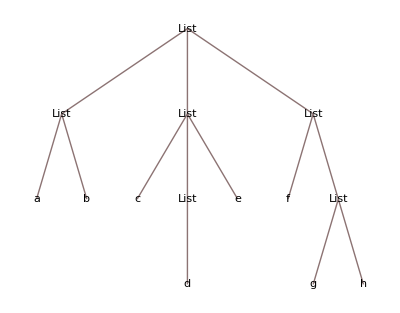

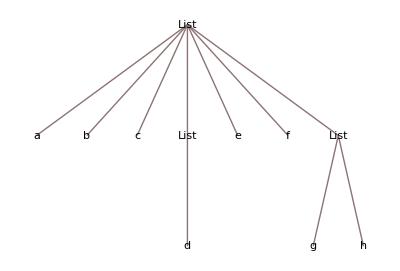

```mathematica
ClearAll["Global`*"]
{{a,b},{c,{d},e},{f,{g,h}}}
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},2]
{{a,b},{c,{d},e},{f,{g,h}}}//TreeForm
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},1]//TreeForm
```